# Extended Hubbard Model

two-orbital Hubbard model with cosine higher bands

## Initialization cells

constant

```mathematica
a=1;
t1=1;
t1dash=0;
t2=0.1;
t2dash=0.4;
mu=0;
```

displacements

```mathematica
delta={a/2{1,√3},a/2{1,-√3},-a{1,0}};
fifthNN={3a{1,0},3/2 a{1,√3},3/2 a{-1,√3},3/2 a{-1,-√3},3/2 a{1,-√3},3a{-1,0}};
```

k vector

```mathematica
k={kx,ky};
```

## SU(4) Hamiltonian

```mathematica
f=Assuming[{kx∈Reals,ky∈Reals},t1*Sum[Exp[ⅈ k.delta[[i]]],{i,1,3}]+t2*Sum[Exp[ⅈ k.fifthNN[[i]]],{i,1,6}]]//ComplexExpand//FullSimplify
```

Cos[kx]+0.2 Cos[3 kx]+Cos[1/2 (kx-√3 ky)]+0.2 Cos[3/2 (kx-√3 ky)]+Cos[1/2 (kx+√3 ky)]+0.2 Cos[3/2 (kx+√3 ky)]+2 ⅈ Cos[(√3 ky)/2] Sin[kx/2]-ⅈ Sin[kx]

```mathematica
g[kx_,ky_]=Abs[f]-0.5//ComplexExpand
```

-0.5+√((Cos[kx]+0.2 Cos[3 kx]+Cos[1/2 (kx-√3 ky)]+0.2 Cos[3/2 (kx-√3 ky)]+Cos[1/2 (kx+√3 ky)]+0.2 Cos[3/2 (kx+√3 ky)])^2+(2 Cos[(√3 ky)/2] Sin[kx/2]-Sin[kx])^2)

```mathematica
Plot3D[g[kx,ky],{kx,-π,π},{ky,-π,π},BoxRatios->{1,1,1},AxesLabel->{"kx","ky","E"}]
```

-Graphics3D-

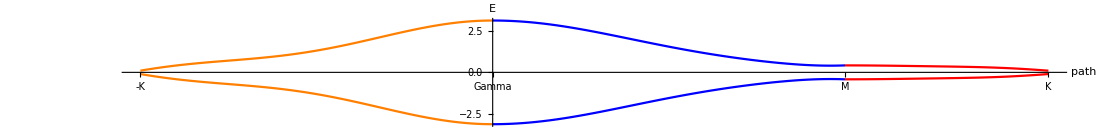

```mathematica
Show[{Plot[{g[kx,kx/(√3)],-g[kx,kx/(√3)]},{kx,-(2π)/3,0},PlotStyle->Orange],Plot[{g[kx,0],-g[kx,0]},{kx,0,(2π)/3},PlotStyle->Blue],Plot[{g[2 π/3,(ky-2 π/3)],-g[2 π/3,(ky-2 π/3)]},{ky,(2π)/3,(2π)/3+(2π)/(3 √3)},PlotStyle->Red]},AxesOrigin->{0,0},PlotRange->{Automatic,Automatic}, AxesLabel->{"path","E"},Ticks->{{{-2 π/3,"-K"},{0,"Gamma"},{(2π)/3,"M"},{(2π)/3+(2π)/(3 √3),"K"}},Automatic},AspectRatio->1/8]
```

## U(1) x SU(2) Hamiltonian

```mathematica
M={{0,0,"A","B"},{0,0,"F",0},{"Aconj","Fconj",0,0},{"Bconj",0,0,0}};
M//MatrixForm
Eigenvalues[M]
```

(0 | 0 | A | B
0 | 0 | F | 0
Aconj | Fconj | 0 | 0
Bconj | 0 | 0 | 0)

{-(√(A Aconj+B Bconj+F Fconj-√(-4 B Bconj F Fconj+(-A Aconj-B Bconj-F Fconj)^2)))/(√2),(√(A Aconj+B Bconj+F Fconj-√(-4 B Bconj F Fconj+(-A Aconj-B Bconj-F Fconj)^2)))/(√2),-(√(A Aconj+B Bconj+F Fconj+√(-4 B Bconj F Fconj+(-A Aconj-B Bconj-F Fconj)^2)))/(√2),(√(A Aconj+B Bconj+F Fconj+√(-4 B Bconj F Fconj+(-A Aconj-B Bconj-F Fconj)^2)))/(√2)}

```mathematica
A=Assuming[{kx∈Reals,ky∈Reals},t1*Sum[Exp[ⅈ k.delta[[i]]],{i,1,3}]+t2*Sum[Exp[ⅈ k.fifthNN[[i]]],{i,1,6}]]//ComplexExpand//FullSimplify
AAconj=A*ComplexExpand[Conjugate[A]]//ComplexExpand //FullSimplify
```

Cos[kx]+0.2 Cos[3 kx]+Cos[1/2 (kx-√3 ky)]+0.2 Cos[3/2 (kx-√3 ky)]+Cos[1/2 (kx+√3 ky)]+0.2 Cos[3/2 (kx+√3 ky)]+2 ⅈ Cos[(√3 ky)/2] Sin[kx/2]-ⅈ Sin[kx]

3.06+0.2 Cos[2 kx]+0.04 Cos[3 kx]+0.2 Cos[4 kx]+0.02 Cos[6 kx]+2. Cos[√3 ky]+0.04 Cos[3 √3 ky]+0.2 Cos[1/2 (kx-3 √3 ky)]+0.2 Cos[1/2 (5 kx-3 √3 ky)]+0.2 Cos[kx-2 √3 ky]+0.2 Cos[kx-√3 ky]+0.04 Cos[3/2 (kx-√3 ky)]+0.2 Cos[2 (kx-√3 ky)]+0.02 Cos[3 (kx-√3 ky)]+0.2 Cos[2 kx-√3 ky]+2. Cos[1/2 (3 kx-√3 ky)]+0.04 Cos[3/2 (3 kx-√3 ky)]+0.2 Cos[1/2 (5 kx-√3 ky)]+0.2 Cos[1/2 (7 kx-√3 ky)]+0.2 Cos[kx+√3 ky]+0.04 Cos[3/2 (kx+√3 ky)]+0.2 Cos[2 (kx+√3 ky)]+0.02 Cos[3 (kx+√3 ky)]+0.2 Cos[2 kx+√3 ky]+2. Cos[1/2 (3 kx+√3 ky)]+0.04 Cos[3/2 (3 kx+√3 ky)]+0.2 Cos[1/2 (5 kx+√3 ky)]+0.2 Cos[1/2 (7 kx+√3 ky)]+0.2 Cos[kx+2 √3 ky]+0.2 Cos[1/2 (kx+3 √3 ky)]+0.2 Cos[1/2 (5 kx+3 √3 ky)]

```mathematica
B=Assuming[{kx∈Reals,ky∈Reals},t2dash*Sum[Exp[ⅈ k.fifthNN[[i]]],{i,1,6}]]//ComplexExpand//FullSimplify
BBconj=B^2//ComplexExpand //FullSimplify
```

0.8 Cos[3 kx]+0.8 Cos[3/2 (kx-√3 ky)]+0.8 Cos[3/2 (kx+√3 ky)]

0.64+0.64 Cos[3 √3 ky]+0.32 Cos[3 (kx-√3 ky)]+Cos[3 kx] (0.64+0.64 Cos[3 kx]+1.28 Cos[3/2 (kx-√3 ky)]+1.28 Cos[3/2 (kx+√3 ky)])+0.32 Cos[3 (kx+√3 ky)]

```mathematica
F=Assuming[{kx∈Reals,ky∈Reals},-t2dash*Sum[Exp[ⅈ k.fifthNN[[i]]],{i,1,6}]]//ComplexExpand//FullSimplify
FFconj=F^2//ComplexExpand //FullSimplify
```

-0.8 Cos[3 kx]-0.8 Cos[3/2 (kx-√3 ky)]-0.8 Cos[3/2 (kx+√3 ky)]

0.64+0.64 Cos[3 √3 ky]+0.32 Cos[3 (kx-√3 ky)]+Cos[3 kx] (0.64+0.64 Cos[3 kx]+1.28 Cos[3/2 (kx-√3 ky)]+1.28 Cos[3/2 (kx+√3 ky)])+0.32 Cos[3 (kx+√3 ky)]

```mathematica
mag=AAconj+BBconj+FFconj
```

(0.+0. ⅈ)+Cos[kx]^2+0.4 Cos[kx] Cos[3 kx]+1.32 Cos[3 kx]^2+2 Cos[kx] Cos[1/2 (kx-√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx-√3 ky)]+Cos[1/2 (kx-√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx-√3 ky)]+2.64 Cos[3 kx] Cos[3/2 (kx-√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx-√3 ky)]+1.32 Cos[3/2 (kx-√3 ky)]^2+2 Cos[kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx+√3 ky)]+2 Cos[1/2 (kx-√3 ky)] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3/2 (kx-√3 ky)] Cos[1/2 (kx+√3 ky)]+Cos[1/2 (kx+√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx+√3 ky)]+2.64 Cos[3 kx] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx+√3 ky)]+2.64 Cos[3/2 (kx-√3 ky)] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx+√3 ky)] Cos[3/2 (kx+√3 ky)]+1.32 Cos[3/2 (kx+√3 ky)]^2+4 Cos[(√3 ky)/2]^2 Sin[kx/2]^2-4 Cos[(√3 ky)/2] Sin[kx/2] Sin[kx]+Sin[kx]^2

```mathematica
g2[kx_,ky_]=(-√(mag-√(-4*BBconj*FFconj+mag^2)))/(√2)
```

-1/(√2)(√((0.+0. ⅈ)+Cos[kx]^2+0.4 Cos[kx] Cos[3 kx]+1.32 Cos[3 kx]^2+2 Cos[kx] Cos[1/2 (kx-√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx-√3 ky)]+Cos[1/2 (kx-√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx-√3 ky)]+2.64 Cos[3 kx] Cos[3/2 (kx-√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx-√3 ky)]+1.32 Cos[3/2 (kx-√3 ky)]^2+2 Cos[kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx+√3 ky)]+2 Cos[1/2 (kx-√3 ky)] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3/2 (kx-√3 ky)] Cos[1/2 (kx+√3 ky)]+Cos[1/2 (kx+√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx+√3 ky)]+2.64 Cos[3 kx] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx+√3 ky)]+2.64 Cos[3/2 (kx-√3 ky)] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx+√3 ky)] Cos[3/2 (kx+√3 ky)]+1.32 Cos[3/2 (kx+√3 ky)]^2+4 Cos[(√3 ky)/2]^2 Sin[kx/2]^2-4 Cos[(√3 ky)/2] Sin[kx/2] Sin[kx]+Sin[kx]^2-√(-4 ((0.+0. ⅈ)+0.64 Cos[3 kx]^2+1.28 Cos[3 kx] Cos[3/2 (kx-√3 ky)]+0.64 Cos[3/2 (kx-√3 ky)]^2+1.28 Cos[3 kx] Cos[3/2 (kx+√3 ky)]+1.28 Cos[3/2 (kx-√3 ky)] Cos[3/2 (kx+√3 ky)]+0.64 Cos[3/2 (kx+√3 ky)]^2)^2+((0.+0. ⅈ)+Cos[kx]^2+0.4 Cos[kx] Cos[3 kx]+1.32 Cos[3 kx]^2+2 Cos[kx] Cos[1/2 (kx-√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx-√3 ky)]+Cos[1/2 (kx-√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx-√3 ky)]+2.64 Cos[3 kx] Cos[3/2 (kx-√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx-√3 ky)]+1.32 Cos[3/2 (kx-√3 ky)]^2+2 Cos[kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx+√3 ky)]+2 Cos[1/2 (kx-√3 ky)] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3/2 (kx-√3 ky)] Cos[1/2 (kx+√3 ky)]+Cos[1/2 (kx+√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx+√3 ky)]+2.64 Cos[3 kx] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx+√3 ky)]+2.64 Cos[3/2 (kx-√3 ky)] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx+√3 ky)] Cos[3/2 (kx+√3 ky)]+1.32 Cos[3/2 (kx+√3 ky)]^2+4 Cos[(√3 ky)/2]^2 Sin[kx/2]^2-4 Cos[(√3 ky)/2] Sin[kx/2] Sin[kx]+Sin[kx]^2)^2)))

```mathematica
Plot3D[g2[kx,ky],{kx,-π,π},{ky,-π,π},BoxRatios->{1,1,1},AxesLabel->{"kx","ky","E"}]
```

-Graphics3D-

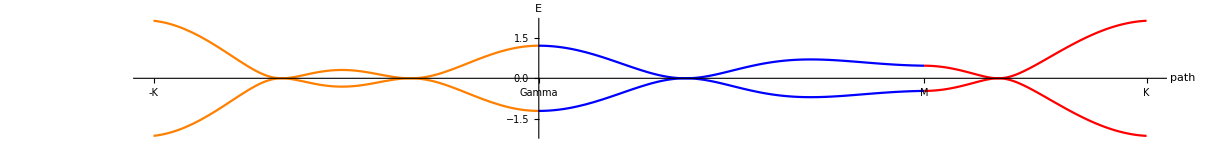

```mathematica
Show[{Plot[{g2[kx,kx/(√3)],-g2[kx,kx/(√3)]},{kx,-(2π)/3,0},PlotStyle->Orange],Plot[{g2[kx,0],-g2[kx,0]},{kx,0,(2π)/3},PlotStyle->Blue],Plot[{g2[2 π/3,(ky-2 π/3)],-g2[2 π/3,(ky-2 π/3)]},{ky,(2π)/3,(2π)/3+(2π)/(3 √3)},PlotStyle->Red]},AxesOrigin->{0,0},PlotRange->{Automatic,Automatic}, AxesLabel->{"path","E"},Ticks->{{{-2 π/3,"-K"},{0,"Gamma"},{(2π)/3,"M"},{(2π)/3+(2π)/(3 √3),"K"}},Automatic},AspectRatio->1/8]
```